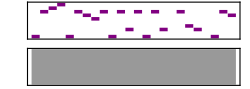

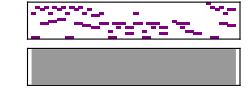

```mathematica
x=0.4;
part1=Sound[{
SoundNote["D5",x,"Piano"],
SoundNote["F5",x,"Piano"],
SoundNote["E5",x,"Piano"],
SoundNote["F5",x,"Piano"],
SoundNote["D5",x,"Piano"],
SoundNote["F5",x,"Piano"],
SoundNote["E5",x,"Piano"],
SoundNote["F5",x,"Piano",SoundVolume->0.25],

SoundNote["D5",x,"Piano"],
SoundNote["F5",x,"Piano"],
SoundNote["E5",x,"Piano"],
SoundNote["F5",x,"Piano"],
SoundNote["D5",x,"Piano"],
SoundNote["E5",x,"Piano"],
SoundNote["C#5",2x,"Piano"],

SoundNote["D5",x,"Piano"],
SoundNote["A4",x,"Piano"],
SoundNote["F4",x,"Piano"],
SoundNote["A4",x,"Piano"],
SoundNote["G4",x,"Piano"],
SoundNote["A4",x,"Piano"],
SoundNote["G4",2x,"Piano"],

SoundNote["D5",x,"Piano"],
SoundNote["A4",x,"Piano"],
SoundNote["F4",x,"Piano"],
SoundNote["A4",x,"Piano"],
SoundNote["G4",x,"Piano"],
SoundNote["A4",x,"Piano"],
SoundNote["G4",2x,"Piano"],
SoundNote[None,x],

SoundNote["Bb4",x,"Piano"],
SoundNote["A4",x,"Piano"],
SoundNote["G4",x,"Piano"],
SoundNote["A4",x,"Piano"],
SoundNote["F4",x,"Piano"],
SoundNote["E4",2x,"Piano"],
SoundNote[None,x],

SoundNote["G5",x,"Piano"],
SoundNote["F5",x,"Piano"],
SoundNote["E5",x,"Piano"],
SoundNote["F5",x,"Piano"],
SoundNote["D5",x,"Piano"],
SoundNote["E5",2x,"Piano"]

}];

bassline1=Sound[{
SoundNote["D4",2x,"Piano"],
SoundNote["A4",2x,"Piano"],
SoundNote["Bb4",2x,"Piano"],
SoundNote["B4",2x,"Piano"],
SoundNote["D4",2x,"Piano"],
SoundNote["A4",2x,"Piano"],
SoundNote["G#4",2x,"Piano"],
SoundNote["G4",2x,"Piano"],
SoundNote["A4",2x,"Piano"],
SoundNote["D4",2x,"Piano"],
SoundNote["A4",2x,"Piano"],
SoundNote["E4",2x,"Piano"],
SoundNote["A4",2x,"Piano"],
SoundNote["D4",2x,"Piano"],
SoundNote["A4",2x,"Piano"],
SoundNote["E4",2x,"Piano"],
SoundNote[None,2x],
SoundNote["A4",2x,"Piano"],
SoundNote["F4",2x,"Piano"],
SoundNote["E4",2x,"Piano"],
SoundNote[None,2x],
SoundNote["D4",2x,"Piano"],
SoundNote["A4",2x,"Piano"],
SoundNote["G#4",2x,"Piano"]
}]

Sound[{
Sound[part1,{0,48x}],Sound[bassline1,{0,48x},SoundVolume->0.5]
}]
```

48.

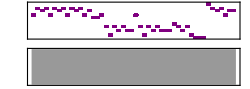

```mathematica
19.2/.4
```

```mathematica
part2=Sound[{
SoundNote["D5",x,"Piano"],
SoundNote["F5",x,"Piano"],
SoundNote["E5",x,"Piano"],
SoundNote["F5",x,"Piano"],
SoundNote["D5",x,"Piano"],
SoundNote["F5",x,"Piano"],
SoundNote["E5",x,"Piano"],
SoundNote["F5",x,"Piano",SoundVolume->0.25],

SoundNote["D5",x,"Piano"],
SoundNote["F5",x,"Piano"],
SoundNote["E5",x,"Piano"],
SoundNote["F5",x,"Piano"],
SoundNote["D5",x,"Piano"],
SoundNote["E5",x,"Piano"],
SoundNote["C#5",2x,"Piano"]
}]
```